```mathematica
(*System information*)
```

```mathematica
data = {M->2, m->1, l->3, g->9.81};
```

```mathematica
(*Lagrangian Dynamics Formulation*)
```

```mathematica
KE = Simplify[Expand[1/2*(M*x'[t]^2+m*((D[x[t]-l*Sin[θ[t]], t]^2)+D[l*Cos[θ[t]], t]^2))]];
PE = m*g*l*Cos[θ[t]];
Lagrangian = KE-PE;
```

```mathematica
eq1 = Simplify[D[D[Lagrangian, x'[t]],t]-D[Lagrangian, x[t]]-fcart];
eq2 = Simplify[D[D[Lagrangian, θ'[t]],t]-D[Lagrangian, θ[t]]];
dyn = {x''[t], θ''[t]}/.Solve[{eq1==0, eq2==0}, {x''[t], θ''[t]}][[1]];
dyneqns = Simplify[dyn/.data];
```

```mathematica
(*The systems configuration space belongs to R^1 X S^1*)
```

```mathematica
q = {x, θ};
```

```mathematica
(*Leaving the system with an initial condition and simulating it to see if the dynamics is correct*)
```

```mathematica
(*Initial conditions*)
```

```mathematica
qinit ={0,π/4};
dqinit = {-0.05, 0};
```

```mathematica
(*qinit ={0,0+0.0000001};
dqinit = {0, 0};*)
```

```mathematica
dyntesteqns = dyneqns/.fcart->0;
```

```mathematica
dyntest = NDSolve[{dyntesteqns[[1]]==x''[t], dyntesteqns[[2]]==θ''[t], {x[0], θ[0]}== qinit, {x'[0], θ'[0]}==dqinit},q,{t, 0, 10}, AccuracyGoal->15, Method->"Adams"][[1]]
```

{x→InterpolatingFunction[…],θ→InterpolatingFunction[…]}

```mathematica
(*Plotting the trajectories*)
```

```mathematica
θplottest = Plot[(θ/.dyntest[[2]])[t], {t, 0, 10}, PlotStyle->Green];
xplottest = Plot[( x/.dyntest[[1]])[t], {t, 0, 10}];
Show[θplottest, xplottest];
```

```mathematica
(*Checking the energy*)
```

```mathematica
Energyexp = (KE+PE)/.data;
```

```mathematica
(*Discretising the solutions*)
```

```mathematica
qtestdat = Table[{(x/.dyntest[[1]])[t], (θ/.dyntest[[2]])[t], (x/.dyntest[[1]])'[t], (θ/.dyntest[[2]])'[t]},{t, 0, 10, 0.01}];
time = Table[t, {t, 0, 10, 0.01}];
```

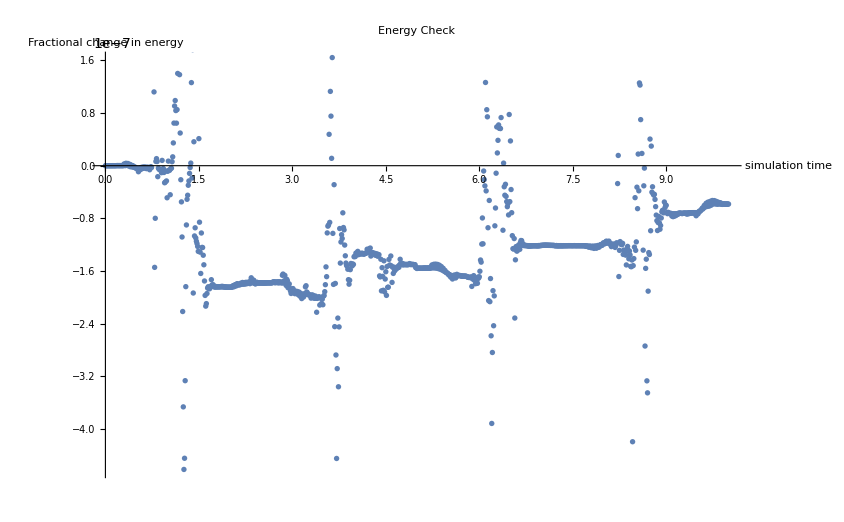

```mathematica
Energytestdat = Table[Energyexp/.Inner[Rule, {x[t], θ[t], x'[t], θ'[t]}, qtestdat[[i]], List], {i, Length[qtestdat]}];
E1 = ConstantArray[Energytestdat[[1]], Dimensions[Energytestdat]];
ListPlot[Transpose[{time, (Energytestdat-E1)/E1}], PlotLabel->"Energy Check", AxesLabel->{"simulation time", "Fractional change in energy"}]
```

```mathematica
(*The mathematical model is consistent*)
```

```mathematica
(*Visualisation*)
```

```mathematica
Manipulate[
cart = Graphics[{Orange,Rectangle[{x+0,0},{x+2,1}]}, PlotRange->{{-4, 4}, {-4, 4}}]/.{x->qtestdat[[i]][[1]], ϕ->qtestdat[[i]][[2]]};
pole = Graphics[{Black, Thick, Line[{{x+1,1/2},{x+1-3*Sin[ϕ],1/2+3*Cos[ϕ]}}]}]/.{x->qtestdat[[i]][[1]], ϕ->qtestdat[[i]][[2]]};
Show[cart, pole]
,{i, 1, Length[qtestdat], 1}]
```

```mathematica
(*State-space model*)
```

```mathematica
(*Generalised coordinates are x->x1, θ->x2, x'->x3, θ'->x4*)
```

```mathematica
sslist = {x[t]->x1, θ[t]->x2, x'[t]->x3, θ'[t]->x4};
```

```mathematica
ssmodel = {x3, x4, (dyneqns/.sslist)[[1]], (dyneqns/.sslist)[[2]]}
```

{x3,x4,-(fcart-3 x4^2 Sin[x2]+4.905 Sin[2 x2])/(-3+Cos[x2]^2),(-0.333333 fcart Cos[x2]-9.81 Sin[x2]+0.5 x4^2 Sin[2 x2])/(-3.+Cos[x2]^2)}

```mathematica
(*Non-linear dynamics model in state-space i.e. x' = f(x)+Σg(x)*u *)
```

```mathematica
(*SSmodel, Drift and Control components*)
```

```mathematica
ffun =ssmodel/.fcart->0;
gfun =Table[Coefficient[ssmodel[[i]], fcart],{i, 4}];
```

```mathematica
(*Checking the equilibrium states*)
```

```mathematica
Solve[ffun=={0,0,0,0},{x1, x2, x3, x4}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x2→-3.14159,x3→0.,x4→0.},{x2→0.,x3→0.,x4→0.},{x2→3.14159,x3→0.,x4→0.}}

```mathematica
(*These are the expected equilibrium states*)
```

```mathematica
(*Linearise the system about the unstable equilibrium state {0,0,0,0}*)
```

```mathematica
(*Assuming small oscillations*)
```

```mathematica
(*Matrices of the linear system*)
```

```mathematica
Amat = D[ssmodel, {{x1, x2, x3, x4}}]/.{x1->0,x2->0,x3->0,x4->0};
bvec = D[ssmodel, {fcart}]/.{x1->0,x2->0,x3->0,x4->0};
```

```mathematica
Ammatdash = Simplify[Amat+Transpose[{bvec}].{{k1, k2, k3, k4}}];
```

```mathematica
(*Now we need to place the poles of Ammatdash such that the system remains stable*)
```

```mathematica
characteristicpoly = Det[Ammatdash-λ*IdentityMatrix[4]];
```

```mathematica
clist = Reverse[CoefficientList[characteristicpoly,λ]]
```

{1,-k3/2-0.166667 k4,-4.905-k1/2-0.166667 k2,1.635 k3,0.+1.635 k1}

```mathematica
(*Use the Rouths array to tune the gain values. Or is there any other way*)
```

```mathematica
(*Full state feedback is not equivalent to PID. Read more about this.*)
```

```mathematica
(*Cascaded control loop*)
```

```mathematica
(*1D learning controller example*)
```

```mathematica
(*So these are the gains. check the eigen values*)
```

```mathematica
(*The coefficients as obtained from the Rouths criteria*)
```

{ α > 0, α β - γ > 0, δ > 0, (α β - γ) γ - α^2 δ >0} 
Choosing the values based on the above rules

```mathematica
(*{α, β, γ, δ} = {1, 4, 2, 2};*)
{α, β, γ, δ} = {10, 50, 50, 20};
tempsol = {Solve[clist[[4]]==γ, k3][[1,1]], Solve[clist[[5]]==δ, k1][[1,1]]};
tempsol2 = Solve[{(clist/.tempsol)[[2]]==α,(clist/.tempsol)[[3]]==β}, {k2, k4}][[1]];
Solve[(characteristicpoly/.tempsol/.tempsol2)==0, λ]
```

{{λ→-4.42032-4.43865 ⅈ},{λ→-4.42032+4.43865 ⅈ},{λ→-0.579678-0.416708 ⅈ},{λ→-0.579678+0.416708 ⅈ}}

```mathematica
(*We have placed all the poles in the LHP successfully*)
```

```mathematica
(*Now let us simulate the system with these gains*)
```

```mathematica
(*The state dependent controller, u = K*x, where u=fcart, we use this controller obtained from linearisation to stabilise the non-linear system*)
```

```mathematica
gains = Join[tempsol, tempsol2];
controlinput = {fcart->{k1, k2, k3, k4}.{x1, x2, x3, x4}}/.gains;
```

```mathematica
sslisttot = {x1->x1[t], x2->x2[t], x3->x3[t], x4->x4[t]};
```

```mathematica
controlledssmodel = Simplify[ssmodel/.controlinput]/.sslisttot;
```

```mathematica
(*Case-1: Integrate the system for small errors about the top equilibrium point, say θ=0.01 radians and θ' = 0*)
```

```mathematica
ssinit = {0,45*π/180,0,0};
```

```mathematica
tf = 2;
controlsyssim = NDSolve[{x1'[t]== controlledssmodel[[1]], x2'[t]== controlledssmodel[[2]], x3'[t]== controlledssmodel[[3]], x4'[t]== controlledssmodel[[4]], {x1[0], x2[0], x3[0], x4[0]}==ssinit}, {x1, x2, x3, x4}, {t, 0, tf}][[1]];
```

```mathematica
(*Experimentally found that we can control errors in angle upto 50 degrees! with this linear controller*)
```

```mathematica
qcontroldat = Table[{(x1/.controlsyssim)[t], (x2/.controlsyssim)[t], (x3/.controlsyssim)[t], (x4/.controlsyssim)[t]},{t, 0,tf, 0.01}];
```

```mathematica
xlimit = Max[Abs[qcontroldat[[1;;]]]]
```

17.7567

```mathematica
xlimit=10
```

10

```mathematica
cartpoleman = Manipulate[
cart = Graphics[{Orange,Rectangle[{x+0,0},{x+2,1}]}, PlotRange->{{-xlimit,xlimit}, {-5, 5}}]/.{x->qcontroldat[[i]][[1]], ϕ->qcontroldat[[i]][[2]]};
pole = Graphics[{Thick, Line[{{x+1,1/2},{x+1-3*Sin[ϕ],1/2+3*Cos[ϕ]}}]}]/.{x->qcontroldat[[i]][[1]], ϕ->qcontroldat[[i]][[2]]};
Show[cart, pole]
,{i, 1, Length[qcontroldat], 1}]
```

```mathematica
(*Tune the controller for required characteristics*)
```

```mathematica
(*Control input*)
```

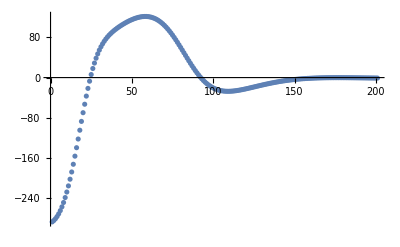

```mathematica
ListPlot[Table[({k1, k2, k3, k4}/.gains).qcontroldat[[i]], {i, Length[qcontroldat]}], PlotRange->All]
```

```mathematica
(*Saving the manipulate as an animation*)
```

```mathematica
(*ManToGif[man_,name_String,step_Integer]:=Export[name<>".gif",Import[Export[FileNameJoin[{NotebookDirectory[],"cartpole.avi"}],man],"ImageList"][[1;;-1;;step]]];
ManToGif[cartpoleman,FileNameJoin[{NotebookDirectory[],"cartpole"}],1];*)
```

```mathematica
(*Note that this is an full state asymptotic stabilising controller and hence brings all the states back to 0 and not just θ error. It tries to hold all the positions*)
```

```mathematica
(*Linear Quadratic Regulator*)
```

```mathematica
(*We need to have a discretised system*)
```

```mathematica
(*We start with Q as diagonal matrix and R as 1*)
```

```mathematica
Qval = DiagonalMatrix[{1,100,10,1}];
Rval = {{1}};
```

```mathematica
bvec2 = Transpose[{bvec}];
```

```mathematica
(*Assuming no constraint on the terminal state*)
```

```mathematica
(*Assuming an asymptotic solution exists for the Ricatti Differential equations and hence solving the Algebraic Ricatti Equations*)
```

```mathematica
Pmat = RiccatiSolve[{Amat, bvec2}, {Qval, Rval}]
```

{{4.99816,-50.9107,7.49079,-28.4724},{-50.9107,2497.83,-225.987,1295.45},{7.49079,-225.987,32.2505,-126.74},{-28.4724,1295.45,-126.74,685.686}}

```mathematica
(*Using the Pmat for the controller*)
```

```mathematica
LQRgains = (-1*Transpose[bvec2].Pmat);
```

```mathematica
(*Verifying the Eigen values*)
```

```mathematica
Eigenvalues[Amat+Transpose[{bvec}].LQRgains]
```

{-2.40852+0.18763 ⅈ,-2.40852-0.18763 ⅈ,-0.832479+0. ⅈ,-0.336525+0. ⅈ}

```mathematica
LQRcontrolinput = {fcart->LQRgains.{x1, x2, x3, x4}};
LQRcontrolledssmodel = Flatten[Simplify[ssmodel/.LQRcontrolinput]/.sslisttot];
```

```mathematica
(*Case-2: Integrate the system for small errors about the top equilibrium point*)
```

```mathematica
ssinit = {0,30*π/180,0,0};
```

```mathematica
tf = 20;
LQRcontrolsyssim = NDSolve[{x1'[t]==LQRcontrolledssmodel[[1]], x2'[t]==LQRcontrolledssmodel[[2]], x3'[t]==LQRcontrolledssmodel[[3]], x4'[t]==LQRcontrolledssmodel[[4]], {x1[0], x2[0], x3[0], x4[0]}==ssinit}, {x1, x2, x3, x4},{t, 0, tf}, AccuracyGoal->15, Method->"Adams"][[1]];
```

```mathematica
LQRqcontroldat = Table[{(x1/.LQRcontrolsyssim)[t], (x2/.LQRcontrolsyssim)[t], (x3/.LQRcontrolsyssim)[t], (x4/.LQRcontrolsyssim)[t]},{t, 0,tf, 0.01}];
```

```mathematica
LQRqcontroldat[[-1]]
```

{-0.0227562,0.00027203,0.0076574,-0.0000914892}

```mathematica
(*Experimentally found that we can control errors in angle upto 61 degrees! with this linear controller*)
```

```mathematica
xlimit = Max[Abs[LQRqcontroldat[[1;;]]]]
```

5.68353

```mathematica
xlimit =10
```

10

```mathematica
LQRcartpoleman = Manipulate[
cart = Graphics[{Orange,Rectangle[{x+0,0},{x+2,1}]}, PlotRange->{{-xlimit,xlimit}, {-5, 5}}]/.{x->LQRqcontroldat[[i]][[1]], ϕ->LQRqcontroldat[[i]][[2]]};
pole = Graphics[{Thick, Line[{{x+1,1/2},{x+1-3*Sin[ϕ],1/2+3*Cos[ϕ]}}]}]/.{x->LQRqcontroldat[[i]][[1]], ϕ->LQRqcontroldat[[i]][[2]]};
Show[cart, pole]
,{i, 1, Length[LQRqcontroldat], 1}]
```

```mathematica
(*Control input*)
```

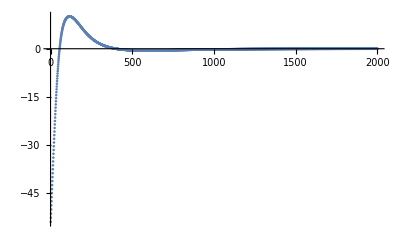

```mathematica
ListPlot[Table[Flatten[(LQRgains)].LQRqcontroldat[[i]], {i, Length[LQRqcontroldat]}], PlotRange->All]
```

```mathematica
(*So with tuning I could go till 95 degrees and now Im convinced that if you can tune further you can get better results. But the thing is the control input required is also shooting up as seen here which is unpractical also it seems like to takes higher time to do the required stabilisation*)
```

```mathematica
(*https://ocw.mit.edu/courses/mechanical-engineering/2-154-maneuvering-and-control-of-surface-and-underwater-vehicles-13-49-fall-2004/lecture-notes/lec19.pdf*)
```

```mathematica
(*Now lets try a feedback linearisation method*)
```

```mathematica
(*Claim: Underactuated systems are not completely feedback linearisable but can be partially feedback linearised*)
```

```mathematica
(*Swing-up control*)
```

```mathematica
(*We clearly see that {0,0} is an unstable point, but cannot see the homoclinic orbit here*)
```

```mathematica
Edesired = m*g*l/.data;
Edash = 1/2*m*l^2*θ'[t]^2+m*g*l*Cos[θ[t]]-Edesired;

Edashdot = Simplify[D[Edash, t]/.{θ''[t]-> dyneqns[[2]]}];
tempfcart = Solve[(Together[Edashdot]+u*Cos[θ[t]]*θ'[t])==0, fcart][[1]];
tempEshapeddot = FullSimplify[Edashdot/.tempfcart];
```

```mathematica
(*Now we have shaped the energy. Now choose u in such a way that Edash will decay over time*)
```

```mathematica
urule = {u->Simplify[k*Cos[θ[t]]*θ'[t]*Edash]};
```

```mathematica
kval = 400;
temp2fcart = Simplify[tempfcart/.urule]/.sslist/.data/.k->kval;
```

```mathematica
shapedssmodel = ssmodel/.temp2fcart/.sslisttot;
```

```mathematica
ssinit = {0,180*π/180,0,0};
```

```mathematica
(*We can see the effect of solvers on the top position holding capacity. Solvers like ADAMS hold it pretty well (takes a higher amount of time to compute though), whereas no solver will easily drop it and are prone to numnerical errors*)
```

```mathematica
(*NDSolve[{x'[t]==Abs[u[t]],u[t]==Sin[t],y[t]==x[t],y[0]==10},{x,y,u},{t,0,10},Method->{"DAEInitialization"->{"Collocation","CollocationDirection"->"Forward"}}]*)
```

```mathematica
tf = 40;
kp = 1;
kd = 1;
shapedcontrolsyssim = NDSolve[{x1'[t]==shapedssmodel[[1]], x2'[t]==shapedssmodel[[2]], x3'[t]==shapedssmodel[[3]]-kp*x1[t]-kd*x3[t], x4'[t]==shapedssmodel[[4]], {x1[0], x2[0], x3[0], x4[0]}==ssinit}, {x1, x2, x3, x4},{t, 0, tf}, AccuracyGoal->15][[1]]
```

NDSolve::mxst: Maximum number of 97419 steps reached at the point t == 32.8323.

{x1→InterpolatingFunction[{{0., 32.8323}}, <>],x2→InterpolatingFunction[{{0., 32.8323}}, <>],x3→InterpolatingFunction[{{0., 32.8323}}, <>],x4→InterpolatingFunction[{{0., 32.8323}}, <>]}

```mathematica
shapedqcontroldat = Table[{(x1/.shapedcontrolsyssim)[t], (x2/.shapedcontrolsyssim)[t], (x3/.shapedcontrolsyssim)[t], (x4/.shapedcontrolsyssim)[t]},{t, 0,30, 0.01}];
```

```mathematica
xlimit = Max[Abs[shapedqcontroldat[[1;;]]]]
```

12.5919

```mathematica
LQRcartpoleman = Manipulate[
cart = Graphics[{Blue,Rectangle[{x+0,0},{x+2,1}]}, PlotRange->{{-10,10}, {-5, 5}}]/.{x->shapedqcontroldat[[i]][[1]], ϕ->shapedqcontroldat[[i]][[2]]};
pole = Graphics[{Thick, Line[{{x+1,1/2},{x+1-3*Sin[ϕ],1/2+3*Cos[ϕ]}}]}]/.{x->shapedqcontroldat[[i]][[1]], ϕ->shapedqcontroldat[[i]][[2]]};
Show[cart, pole]
,{i, 1, Length[shapedqcontroldat], 1}]
```

```mathematica
(*Control input*)
```

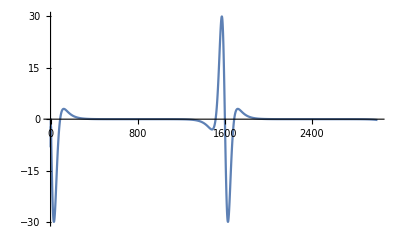

```mathematica
ListLinePlot[Table[fcart/.temp2fcart/.Inner[Rule, {x1, x2, x3, x4},shapedqcontroldat[[i]], List],{i, Length[shapedqcontroldat]}], PlotRange->All]
```

```mathematica
(*Phase portrait of the modified system*)
```

```mathematica
θssshaped = Simplify[{ssmodel[[2]], ssmodel[[4]]}/.temp2fcart/.k->kval];
sysplot2 = StreamPlot[θssshaped,{x2,-π,5π},{x4,-5,5}, StreamPoints->Fine, StreamStyle->"PinDart", PerformanceGoal->"Quality", StreamPoints->{{{{2π-0.1,0},Orange},Automatic}}];
```

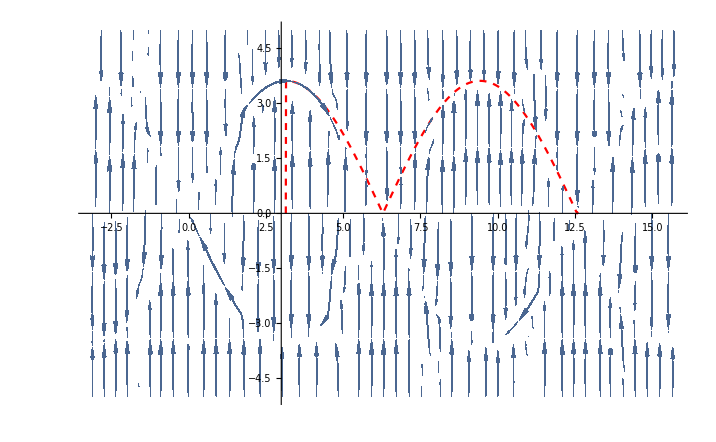

```mathematica
Show[ListLinePlot[Transpose[Join[{shapedqcontroldat[[;;,2]]},{shapedqcontroldat[[;;,4]]}]], PlotRange->All, PlotStyle->{Dashed, Red}], sysplot2, PlotRange->All]
```

```mathematica
θdyn = {ssmodel[[2]], ssmodel[[4]]}/.fcart->0;
sysplot = StreamPlot[θdyn,{x2,-π,5π},{x4,-2π,2π},StreamPoints->{{{{2π-0.1,0},Orange}, {{4π-0.1,0},Orange},Automatic}}, StreamPoints->Fine, PerformanceGoal->"Quality"];
```

```mathematica
(*StreamPlot[{-1-x^2+y,1+x-y^2},{x,-3,3},{y,-3,3},StreamPoints->{{{{1,0},Red},{{-1,-1},Green},Automatic}}]*)
```

```mathematica
Show[ListLinePlot[Transpose[Join[{shapedqcontroldat[[;;,2]]},{shapedqcontroldat[[;;,4]]}]], PlotRange->All, PlotStyle->{Dashed, Red}], sysplot, PlotRange->All];
```

```mathematica
(*This controller goes there but does not stabilise it. So we need to switch once the controller reaches the top vicinity. We should know how to switch to such a controller and simulate it*)
```

```mathematica
(*Now for the final method, we do trajectory optimisation with LQR*)
```

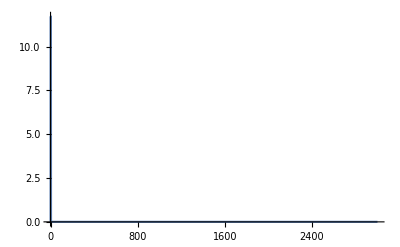

```mathematica
ListLinePlot[Table[u/.urule/.k->kval/.data/.sslist/.Inner[Rule, {x1, x2, x3, x4},shapedqcontroldat[[i]], List],{i, Length[shapedqcontroldat]}], PlotRange->All]
```

```mathematica
(*The controller works as expected, it pushes the system to the homoclinic orbit and then the system moves to the steady state. Note that we need a stabiliser to stabilise the system at 0. Read more from Russ Tedrake's book*)
```

```mathematica
(*Trajectory optimization with LQR*)
```

```mathematica
(*Data imported after optimisation from MATLAB*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
qcontroldattrajopt = Import["trajoptdatx.csv"];
```

```mathematica
cartpolemantrajopt = Manipulate[
cart = Graphics[{Blue,Rectangle[{x+0,0},{x+2,1}]}, PlotRange->{{-5,5}, {-5, 5}}]/.{x->qcontroldattrajopt[[i]][[1]], ϕ->qcontroldattrajopt[[i]][[2]]};
pole = Graphics[{Thick, Line[{{x+1,1/2},{x+1-3*Sin[ϕ],1/2+3*Cos[ϕ]}}]}]/.{x->qcontroldattrajopt[[i]][[1]], ϕ->qcontroldattrajopt[[i]][[2]]};
Show[cart, pole]
,{i, 1, Length[qcontroldattrajopt], 1}]
```

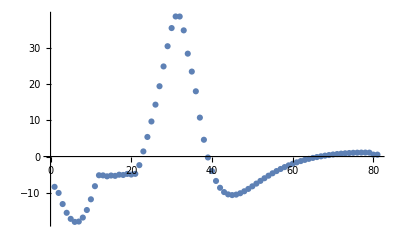

```mathematica
controldat = Import["trajoptdatu.csv"];
ListPlot[Flatten[controldat], PlotRange->All]
```

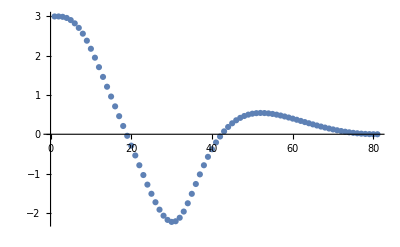

```mathematica
ListPlot[qcontroldattrajopt[[;;, 1]], PlotRange->All]
```

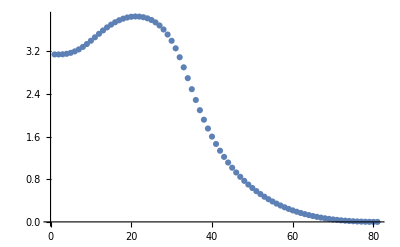

```mathematica
ListPlot[qcontroldattrajopt[[;;, 2]], PlotRange->All]
```

```mathematica
(*So these are the soltions obtained at the collocation points of the transcription. Now we need to interpolate these solutions*)
```

```mathematica
(*Interpolation*)
```

Control input was assumed to be linear in nature and hence will be its interpolation as,
β = (-1/h) * (u(k) - u(k-1))
u(t) = u(k) + δ(k) β
where δk = t - tk

Where as since the dynamics was assumed to be linear, the state approximation would be quadratic
γk = -1/(2*h) * (f(k) - f(k+1))
x(t) = x(k) + δk * f(k) + δk^2 *γk

```mathematica
(*Verifying the solution accuracy*)
```

```mathematica
(*We need to interpolate and then use the original dynamics equations to find the difference between these and plot them. Also After we get to this stage, we should check for the h-convergence.*)
```